{1/19,0.188679,0.411523,0.621118,0.806452,0.917431,0.961538,0.990099,0.990099}

{0.952381,0.813008,0.588235,0.377358,0.196078,0.0888889,1/23,1/75,1/150}

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{x→3.05254}}

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{x→3.05144}}

{0.0472388,0.191437,0.411523,0.635463,0.806359,0.910693,0.963773,0.98692,0.995752,0.998748}

{0.952709,0.808404,0.588235,0.364291,0.193453,0.0891927,0.0361687,0.0130544,0.00423795,0.00124873}

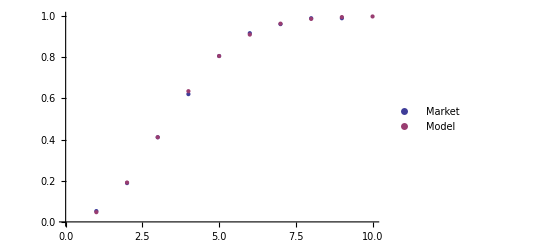

CDF

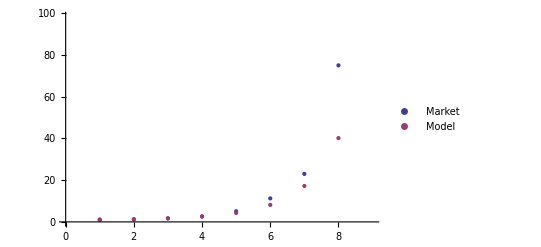

```mathematica
under0=1/{19,5.3,2.43,1.61,1.24,1.09,1.04,1.01,1.01}
over0=1/{1.05,1.23,1.7,2.65,5.1,11.25,23,75,150}
underIntensity0=NSolve[CDF[PoissonDistribution[x],2]==under0[[3]], x]
overIntensity0=NSolve[1-CDF[PoissonDistribution[x],2]==over0[[3]], x]

calUnder0=Evaluate@Table[CDF[PoissonDistribution[x/.underIntensity0[[1]]],k],{k,0,9}]
calOver0=Evaluate@Table[1-CDF[PoissonDistribution[x/.overIntensity0[[1]]],k],{k,0,9}]
ListPlot[{under0,calUnder0},PlotLegends->{"Market", "Model"}]
CDF
```

{1/24,0.153846,0.411523,0.581395,0.775194,0.892857,0.961538,0.990099,0.990099}

{0.961538,0.847458,0.591716,0.41841,0.224719,0.11236,0.0465116,0.016,1/305}

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{x→3.05254}}

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{x→3.06729}}

{0.0472388,0.191437,0.411523,0.635463,0.806359,0.910693,0.963773,0.98692,0.995752,0.998748}

{0.953453,0.81068,0.591716,0.367841,0.196168,0.0908539,0.0370157,0.0134246,0.00437952,0.00129686}

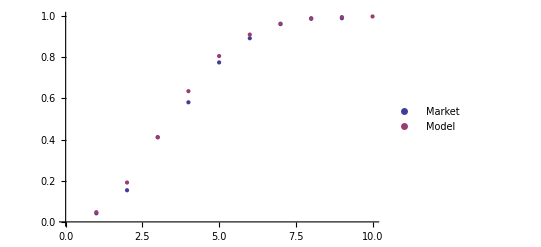

```mathematica
under1=1/{24,6.5,2.43,1.72,1.29,1.12,1.04,1.01,1.01}
over1=1/{1.04,1.18,1.69,2.39,4.45,8.9,21.5,62.5,305}
underIntensity1=NSolve[CDF[PoissonDistribution[x],2]==under1[[3]], x]
overIntensity1=NSolve[1-CDF[PoissonDistribution[x],2]==over1[[3]], x]
calUnder1=Evaluate@Table[CDF[PoissonDistribution[x/.underIntensity1[[1]]],k],{k,0,9}]
calOver1=Evaluate@Table[1-CDF[PoissonDistribution[x/.overIntensity1[[1]]],k],{k,0,9}]
ListPlot[{under1,calUnder1}, PlotLegends->{"Market", "Model"}]
```

### Historic Odds

{0.0786,0.267,0.5266,0.7469,0.881,0.956,0.9859,0.9964,0.9989}

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{x→2.56757}}

{0.0767214,0.273709,0.5266,0.743038,0.881969,0.953312,0.983841,0.99504,0.998634,0.999659}

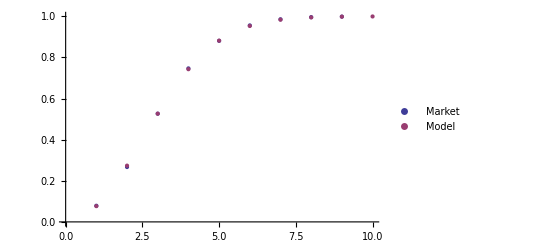

```mathematica
underHist={0.0786,0.267,0.5266,0.7469,0.881,0.956,0.9859,0.9964,0.9989}
underIntensityHist=NSolve[CDF[PoissonDistribution[x],2]==underHist[[3]], x]

calUnderHist=Evaluate@Table[CDF[PoissonDistribution[x/.underIntensityHist[[1]]],k],{k,0,9}]
ListPlot[{underHist,calUnderHist},PlotLegends->{"Market", "Model"}]
```

### Risks

-(Piecewise[{{-(ⅇ^-λ λ^Floor[x])/Gamma[1+Floor[x]], x≥0}, {0, True}}])

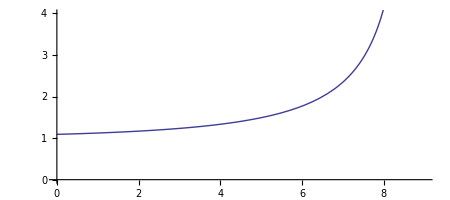

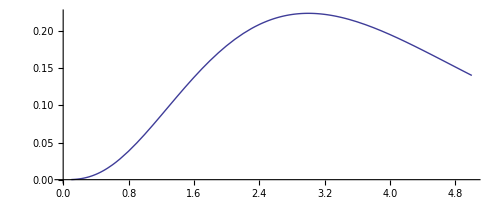

-0.256516

{0.961538,0.847458,0.591716,0.41841,0.224719,0.11236,0.0465116,0.016,1/305}

{1.,0.881356,0.615385,0.435146,0.233708,0.116854,0.0483721,0.01664,0.00340984}

{0.0384615,0.0338983,0.0236686,0.0167364,0.00898876,0.00449438,0.00186047,0.00064,0.000131148}

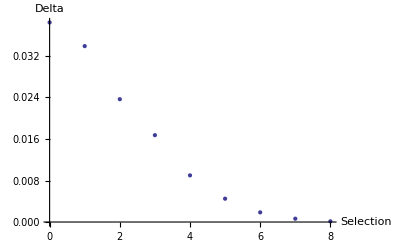

{0.082085,0.205212,0.256516,0.213763,0.133602,0.0668009,0.0278337,0.00994062,0.00310644,0.000862901}

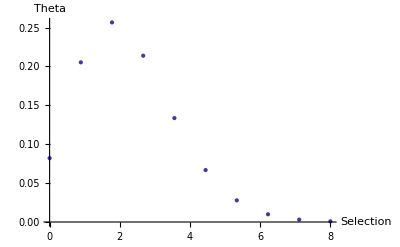

1.625

0.334753

0.32

0.0308876

```mathematica
D[1-CDF[PoissonDistribution[λ],x],λ]
ThetaFunction[λ_, x_]:=-(Piecewise[{{-(ⅇ^-λ λ^Floor[x])/Gamma[1+Floor[x]], x≥0}, {0, True}}])
ParametricPlot[{t,1/(1-CDF[PoissonDistribution[2.5*(9-t)/9],0])}, {t, 0, 9}, ImageSize->Full, PlotRange->{{0,9},{0,4}}]
ParametricPlot[{λ,(ⅇ^-λ λ^Floor[3])/Gamma[1+Floor[3]]}, {λ, 0.1, 5}]
-(ⅇ^-2.5 2.5^Floor[2])/Gamma[1+Floor[2]]
overProbsBeforeGoal=1/{1.04,1.18,1.69,2.39,4.45,8.9,21.5,62.5,305}
overProbsAfterGoal={(overProbsBeforeGoal[[1]]/overProbsBeforeGoal[[1]]), (overProbsBeforeGoal[[2]]/overProbsBeforeGoal[[1]]),(overProbsBeforeGoal[[3]]/overProbsBeforeGoal[[1]]),(overProbsBeforeGoal[[4]]/overProbsBeforeGoal[[1]]),(overProbsBeforeGoal[[5]]/overProbsBeforeGoal[[1]]),(overProbsBeforeGoal[[6]]/overProbsBeforeGoal[[1]]),(overProbsBeforeGoal[[7]]/overProbsBeforeGoal[[1]]),(overProbsBeforeGoal[[8]]/overProbsBeforeGoal[[1]]),(overProbsBeforeGoal[[9]]/overProbsBeforeGoal[[1]])}
deltas={(overProbsAfterGoal[[1]]-overProbsBeforeGoal[[1]]), (overProbsAfterGoal[[2]]-overProbsBeforeGoal[[2]]),(overProbsAfterGoal[[3]]-overProbsBeforeGoal[[3]]),(overProbsAfterGoal[[4]]-overProbsBeforeGoal[[4]]),(overProbsAfterGoal[[5]]-overProbsBeforeGoal[[5]]),(overProbsAfterGoal[[6]]-overProbsBeforeGoal[[6]]),(overProbsAfterGoal[[7]]-overProbsBeforeGoal[[7]]),(overProbsAfterGoal[[8]]-overProbsBeforeGoal[[8]]),(overProbsAfterGoal[[9]]-overProbsBeforeGoal[[9]])}
ListPlot[deltas, AxesLabel->{"Selection", "Delta"}, DataRange->{0, 8}]
thetas = {ThetaFunction[2.5, 0],ThetaFunction[2.5, 1],ThetaFunction[2.5, 2],ThetaFunction[2.5, 3],ThetaFunction[2.5, 4],ThetaFunction[2.5, 5],ThetaFunction[2.5, 6],ThetaFunction[2.5, 7],ThetaFunction[2.5, 8],ThetaFunction[2.5, 9]}
ListPlot[thetas, AxesLabel->{"Selection", "Theta"}, DataRange->{0, 8}]
deltaHedge2For0=deltas[[1]]/deltas[[3]]
residualThetaDeltaHedge2For0=-(thetas[[1]]-deltaHedge2For0*thetas[[3]])
thetaHedge2For0=thetas[[1]]/thetas[[3]]
residualDeltaThetaHedge2For0=deltas[[1]]-thetaHedge2For0*deltas[[3]]
```

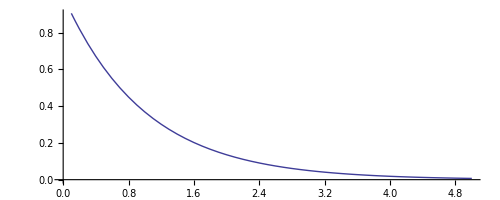

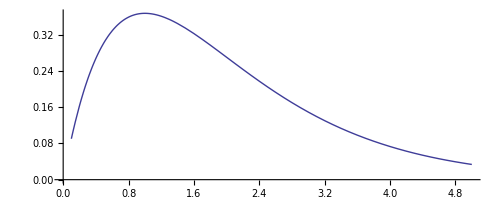

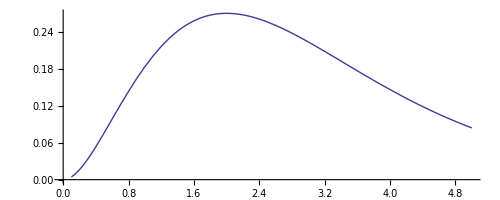

```mathematica
FullSimplify[D[PDF[PoissonDistribution[λ], x], λ]]
```

Piecewise[{{(ⅇ^-λ (x-λ) λ^(-1+x))/(x!), x≥0}, {0, True}}]

```mathematica
D[1/PDF[PoissonDistribution[λ], x], λ]
D[1/CDF[PoissonDistribution[λ], x], λ]
D[1/(1-CDF[PoissonDistribution[λ], x]), λ]
```

-Piecewise[{{(ⅇ^-λ x λ^(-1+x))/(x!)-(ⅇ^-λ λ^x)/(x!), x≥0}, {0, True}}]/((Piecewise[{{(ⅇ^-λ λ^x)/(x!), x≥0}, {0, True}}])^2)

-Piecewise[{{-(ⅇ^-λ λ^Floor[x])/Gamma[1+Floor[x]], x≥0}, {0, True}}]/(Piecewise[{{GammaRegularized[1+Floor[x],λ], x≥0}, {0, True}}])^2

Piecewise[{{-(ⅇ^-λ λ^Floor[x])/Gamma[1+Floor[x]], x≥0}, {0, True}}]/(1-(Piecewise[{{GammaRegularized[1+Floor[x],λ], x≥0}, {0, True}}]))^2